```mathematica
Import["C:\\Users\\Juntao Yu\\Desktop\\Hydro Spectra\\Hg.xlsx"]
```

```mathematica
data={{364.99,365.02},{364.42,365.48},{366.21,366.3},{404.66,404.66},{407.69,407.78},{435.84,435.84},{546.14,546.07},{576.96,576.96},{579.11,579.07}};
```

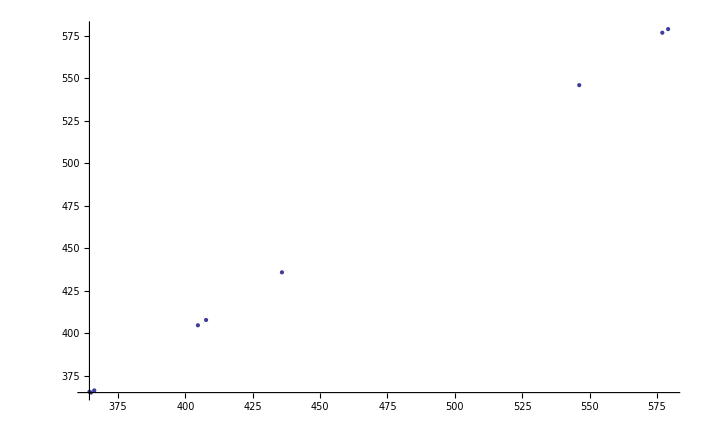

```mathematica
ListPlot[data]
```

```mathematica
a=LinearModelFit[data,x,x]
```

```mathematica
FittedModel[0.8997508367655201+0.9982852883745286 x]
Normal[a]
```

FittedModel[0.899751+0.998285 x]

0.899751+0.998285 x

```mathematica
a["RSquared"]
```

0.999988

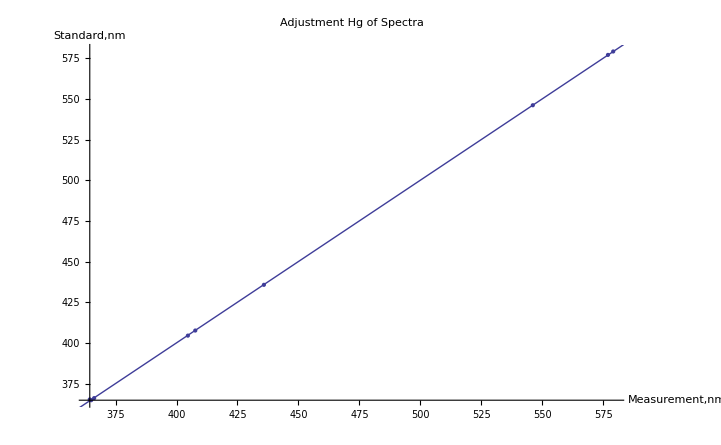

```mathematica
Show[ListPlot[data],Plot[a[x],{x,350,590}],AxesLabel->{"Measurement,nm","Standard,nm"},PlotLabel->Adjustment of Hg Spectra]
```

```mathematica
a[b_]=0.8997508367655201+0.9982852883745286 b;
```

```mathematica
a[409.97]
```

410.167

```mathematica
a[410.08]
```

410.277

```mathematica
a[433.90]
```

434.056

```mathematica
a[434.02]
```

434.176

```mathematica
a[486.01]
```

486.076

```mathematica
a[486.13]
```

486.196

```mathematica
a[656.65]
```

656.424

```mathematica
a[656.82]
```

656.593